# MapReduce in Mathematica

Frederico Meinberg, 2011

## Implementation notes

### Function design for MapReduce

There are the following formats for functions that apply on key:value pairs:

(1) Automatic -> {Map | Reduce -> {Identity},  Combine -> (#1 -> Apply[Flatten[List[##], {1}] &, #2])

(2) f : f[key, value]

(3) {f,g} : f@key -> g@value

(4) {f} : key -> f@value ( same as {Identity, f})

## Examples

```mathematica
Get[ToFileName[NotebookDirectory[],"MapReduce.m"]]
```

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

### Temperatures

```mathematica
ClearAll[t,mr]
```

```mathematica
t[1]=Select[WeatherData["BeloHorizonte" ,"Temperature" ,{2010}],FreeQ[#,Missing]&];
```

```mathematica
t[2]=RandomSample[t[1]];
```

Find the highest and lowest temperatures in each day. The Mapper will reduce the time stamps to day values; The reducer will find maximum and minimum values.

```mathematica
mr[1]=MapReduce[{"Mapper"->(#1[[;;3]]->#2&),"Reducer"->{Max}}];
```

```mathematica
mr[2]=MapReduce[{"Mapper"->(#1[[;;3]]->#2&),"Reducer"->{Min}}];
```

This is how a MapReduce function looks like:

```mathematica
mr[1]
```

Function[Private`records$,SortBy[Join@@((((Null&)[#1];#1)&)[Apply[BinRules[Join@@#2,Total[{##1}]&]&,#1,{1}]]&)/@(((Null&)[#1];#1)&)[BinPartition[(((Null&)[#1];#1)&)[BinRules[Join@@Function[Private`recordnode$,(((Null&)[#1];#1)&)[Apply[#1→(Flatten[{##1},{1}]&)@@#2&,BinRules[(((Null&)[#1];#1)&)[DeleteCases[Nest[Flatten[#1⟦All,2⟧]&,Apply[1→Apply[Rule,Tally[{##1}],{1}]&,Private`recordnode$,{1}],0],_[_,$Failed]]]],{1}]]]/@BinPartition[Private`records$,2],Join]],2]],First]]

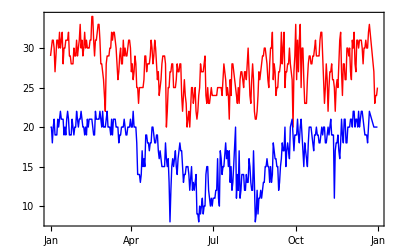

```mathematica
DateListPlot[{List@@@(mr[1][t[2]]),List@@@(mr[2][t[2]])},Joined->True,PlotStyle->{Red,Blue},PlotRange->All]
```

### Word count

The records are lists of words:

```mathematica
ClearAll[t,mr];
```

```mathematica
t[1]=BinPartition[StringSplit[StringReplace[ToLowerCase@ExampleData[{"Text","AeneidLatin"}],Except[WordCharacter]->" "]],1000];
```

Create a MapReduce function. Note how the output of the mapper is a list of key:value pairs for individual words, effectively going one level deeper into the original kv pairs. This is an idiom in Hadoop and implemented using the parameter MapOutputDepth.

```mathematica
mr[1]=MapReduce[{"Mapper"->(1->Rule@@@Tally[{##}]&),"Reducer"->{Total},"MapOutputDepth"->1}];
```

```mathematica
t[2]=mr[1][t[1]];
```

```mathematica
Sort[t[2]]==Sort[Rule@@@Tally@Flatten@t[1]]
```

True

Add a combine step:

```mathematica
mr[2]=MapReduce[{"Mapper"->(1->Rule@@@Tally[{##}]&),"MapOutputDepth"->1,"Combiner"->{Total},"Reducer"->{Total}}];
```

```mathematica
t[3]=mr[2][t[1]];
```

```mathematica
Sort[t[3]]==Sort[Rule@@@Tally@Flatten@t[1]]
```

True